```mathematica
mathnum=80;
```

```mathematica
formnum=99;
```

```mathematica
<<NLOcompare.m
```

FeynCalc 9.0.1. For help, use the documentation center, check out the wiki or write to the mailing list.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

Package-X v1.0.4, by Hiren H. Patel

Contract::shdw: Symbol TraditionalForm`"Contract" appears in multiple contexts TraditionalForm`{"X`IndexAlg`", "FeynCalc`"}; definitions in context TraditionalForm`"X`IndexAlg`" may shadow or be shadowed by other definitions.

DiracMatrix::shdw: Symbol TraditionalForm`"DiracMatrix" appears in multiple contexts TraditionalForm`{"X`Spur`", "FeynCalc`"}; definitions in context TraditionalForm`"X`Spur`" may shadow or be shadowed by other definitions.

For more information, see the

```mathematica
<<renormAmpLarin.res
```

```mathematica
Diagr=<<test/diagrBcnlo.m;
(* Amp =<<AmpBcnlo`; *)
AmpbeforeApart=<<test/AmpbeforeApartBcstarBcWest.m;
AmpafterFire=<<test/AmpafterFireBcstarBcWest.m;
```

```mathematica
DiaCompare[mathnum,formnum,1.5,4.9,175,15^2]
```

0

```mathematica
dianumlist={{1,13},{2,14},{3,31},{4,32},{5,33},{6,34},{7,15},{8,16},{9,43},{10,44},{11,45},{12,46},{13,22},{14,23},{15,24},{16,25},{29,26},{30,27},{31,30},{32,28},{33,29},{34,35},{35,36},{36,37},{37,38},{38,39},{39,40},{40,41},{41,42},{42,17},{43,18},{44,21},{45,19},{46,20},{47,48},{48,50},{49,47},{50,49},{51,57},{52,58},{53,59},{54,60},{55,61},{56,62},{57,63},{58,64},{59,65},{60,67},{61,68},{62,69},{63,70},{64,71},{65,72},{66,73},{67,74},{68,66},{69,88},{70,89},{71,90},{72,91},{73,92},{74,93},{75,94},{76,95},{77,87},{78,97},{79,98},{80,99},{81,100},{82,101},{83,102},{84,103},{85,104},{86,96}};
```

```mathematica
DiaCompareList[dianumlist,1.5,4.9,175,15^2]
```

Checking diagrams with numbers 1 and 13

Checking diagrams with numbers 2 and 14

Checking diagrams with numbers 3 and 31

Checking diagrams with numbers 4 and 32

Checking diagrams with numbers 5 and 33

Checking diagrams with numbers 6 and 34

Checking diagrams with numbers 7 and 15

Checking diagrams with numbers 8 and 16

Checking diagrams with numbers 9 and 43

Checking diagrams with numbers 10 and 44

Checking diagrams with numbers 11 and 45

Checking diagrams with numbers 12 and 46

Checking diagrams with numbers 13 and 22

Checking diagrams with numbers 14 and 23

Checking diagrams with numbers 15 and 24

Checking diagrams with numbers 16 and 25

Checking diagrams with numbers 29 and 26

Checking diagrams with numbers 30 and 27

Checking diagrams with numbers 31 and 30

Checking diagrams with numbers 32 and 28

Checking diagrams with numbers 33 and 29

Checking diagrams with numbers 34 and 35

Checking diagrams with numbers 35 and 36

Checking diagrams with numbers 36 and 37

Checking diagrams with numbers 37 and 38

Checking diagrams with numbers 38 and 39

Checking diagrams with numbers 39 and 40

Checking diagrams with numbers 40 and 41

Checking diagrams with numbers 41 and 42

Checking diagrams with numbers 42 and 17

Checking diagrams with numbers 43 and 18

Checking diagrams with numbers 44 and 21

Checking diagrams with numbers 45 and 19

Checking diagrams with numbers 46 and 20

Checking diagrams with numbers 47 and 48

Checking diagrams with numbers 48 and 50

Checking diagrams with numbers 49 and 47

Checking diagrams with numbers 50 and 49

Checking diagrams with numbers 51 and 57

Checking diagrams with numbers 52 and 58

Checking diagrams with numbers 53 and 59

Checking diagrams with numbers 54 and 60

Checking diagrams with numbers 55 and 61

Checking diagrams with numbers 56 and 62

Checking diagrams with numbers 57 and 63

Checking diagrams with numbers 58 and 64

Checking diagrams with numbers 59 and 65

Checking diagrams with numbers 60 and 67

Checking diagrams with numbers 61 and 68

Checking diagrams with numbers 62 and 69

Checking diagrams with numbers 63 and 70

Checking diagrams with numbers 64 and 71

Checking diagrams with numbers 65 and 72

Checking diagrams with numbers 66 and 73

Checking diagrams with numbers 67 and 74

Checking diagrams with numbers 68 and 66

Checking diagrams with numbers 69 and 88

Checking diagrams with numbers 70 and 89

Checking diagrams with numbers 71 and 90

Checking diagrams with numbers 72 and 91

Checking diagrams with numbers 73 and 92

Checking diagrams with numbers 74 and 93

Checking diagrams with numbers 75 and 94

Checking diagrams with numbers 76 and 95

Checking diagrams with numbers 77 and 87

Checking diagrams with numbers 78 and 97

Checking diagrams with numbers 79 and 98

Checking diagrams with numbers 80 and 99

Checking diagrams with numbers 81 and 100

Checking diagrams with numbers 82 and 101

Checking diagrams with numbers 83 and 102

Checking diagrams with numbers 84 and 103

Checking diagrams with numbers 85 and 104

Checking diagrams with numbers 86 and 96

(0.+1.08551×10^-13 ⅈ) X(42)+(0.+6.54267×10^-15 ⅈ) X(50)+1.02356×10^-8 X(24)-9.21208×10^-8 X(25)-8.18851×10^-8 X(27)-5.8726×10^-10 X(31)+5.28534×10^-9 X(32)-5.8726×10^-10 X(43)+5.28534×10^-9 X(44)+3.30334×10^-9 X(65)-3.30334×10^-9 X(66)-1.8808×10^-7 X(96)

```mathematica
DiaCompareCheck[41,42,1.5,4.9,175,15^2]
```

mathres =

-5.13762×10^-6 eps C[2.25,12.3596,2.25,0,1.5,0]+0.000117889 eps C[24.01,12.3596,76.7444,0,4.9,0]-4.12241×10^-6 eps C[40.96,2.25,76.7444,0,4.9,1.5]-0.00003636 C[24.01,12.3596,76.7444,0,4.9,0]+0.0000423594 C[40.96,2.25,76.7444,0,4.9,1.5]-6.6711×10^-6 eps B(12.3596,0,0)+0.0000109451 eps B(76.7444,4.9,0)+2.22893×10^-6 B(12.3596,0,0)-2.62546×10^-6 B(76.7444,4.9,0)+4.4864×10^-8 A(1.5) eps-2.06623×10^-7 A(4.9) eps-3.93292×10^-7 A(1.5)+6.70125×10^-8 A(4.9)

formres =

-8.3235×10^-6 eps C[2.25,12.3596,2.25,0,1.5,0]+0.000114928 eps C[76.7444,12.3596,24.01,0,4.9,0]+9.92799×10^-6 C[2.25,12.3596,2.25,0,1.5,0]-3.92856×10^-6 C[76.7444,12.3596,24.01,0,4.9,0]-7.03997×10^-6 eps B(12.3596,0,0)+0.0000111727 eps B(76.7444,0,4.9)+2.22893×10^-6 B(12.3596,0,0)-2.62546×10^-6 B(76.7444,0,4.9)+1.70383×10^-7 A(1.5) eps-2.12504×10^-7 A(4.9) eps-3.93292×10^-7 A(1.5)+6.70125×10^-8 A(4.9)

0.+1.08551×10^-13 ⅈ

Diagram  b,cbar->Bc(p3)  bbar,c->Bc(p4):

loading generic model file /home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg/FCFA/FC91/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg/FCFA/FC91/FeynCalc/FeynArts/Models/SMQCD.mod

loading classes model file /home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg/FCFA/FC91/FeynCalc/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

> Top. 1: 1 diagram

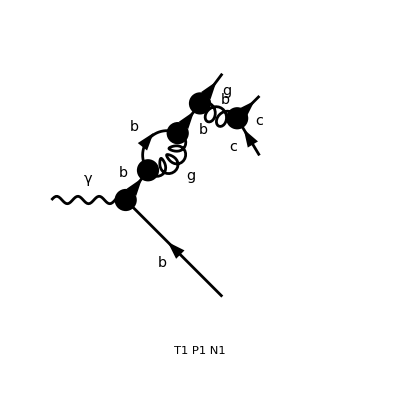

Amplitude after Fire (without PreFactor):

-(4 ⅈ e m g_s^4 (-(4 r^2 s)/m^2-8 r^2+16 r-8) ϵ^(γψ1 OverBar[p3]OverBar[p4]) IntF(1/(-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4])+OverBar[k1]^2+r s),k1))/(27 r^4 s^3 (r (s/m^2-2)+r^2+1))-(4 ⅈ e m g_s^4 (-16 m^2 r^4-(12 r^3 s^2)/m^2+64 m^2 r^3+(16 r^2 s^2)/m^2-96 m^2 r^2+64 m^2 r-16 m^2-8 r^4 s+8 r^3 s+8 r^2 s-8 r s) ϵ^(γψ1 OverBar[p3]OverBar[p4]) IntF(1/(OverBar[k1]^2 (-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4])+OverBar[k1]^2+r s)),k1))/(27 r^4 s^3 (r (s/m^2-2)+r^2+1))+ϵ ((16 ⅈ e m g_s^4 (2 m^2 r^3-6 m^2 r^2+6 m^2 r-2 m^2+2 r^2 s-r s) ϵ^(γψ1 OverBar[p3]OverBar[p4]) IntF(1/(OverBar[k1]^2 (-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4])+OverBar[k1]^2+r s)),k1))/(27 r^3 s^2 (m^2 r^2-2 m^2 r+m^2+r s))-(4 ⅈ e m g_s^4 ((4 r s)/m^2+8 r^2-16 r+8) ϵ^(γψ1 OverBar[p3]OverBar[p4]) IntF(1/(-2 r (OverBar[k1]·OverBar[p3])-2 (OverBar[k1]·OverBar[p4])+OverBar[k1]^2+r s),k1))/(27 r^4 s^3 (r (s/m^2-2)+r^2+1)))

```mathematica
MyDiagrPlot[86]
```